Prelim:

```mathematica
influenzaalpha = 2.321995;
omicronalpha = 2.39;
measlesalpha = 11.35802;
```

```mathematica
influenzaR0 = 2;
omicronR0 = 6;
measlesR0=12;
```

```mathematica
influenzapest = 1-1/influenzaR0;
omicronpest = 1 - 1/omicronR0;
measlespest = 1 - 1/measlesR0;
```

```mathematica
influenzar=0.252;
omicronr=0.378;
measlesr=0.228;
```

```mathematica
z[R0_,α_]:= R0^(1/α) - 1;
```

```mathematica
ρ1[R0_,α_]:=((1 + z[R0,α])/(1 + 2 z[R0, α]));
```

```mathematica
ρ2[R0_,α_]:=((1 + z[R0,α])^2/(1 + 2 z[R0, α]));
```

Plots of the individual terms:

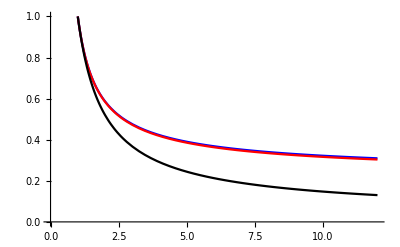

```mathematica
Plot[Evaluate@Table[ρ1[R0, α]^α,{α, {influenzaalpha, omicronalpha, measlesalpha}}],{R0, 1, 12}, PlotRange->{0, Automatic}, PlotStyle->{{Blue}, {Red}, {Black}}]
```

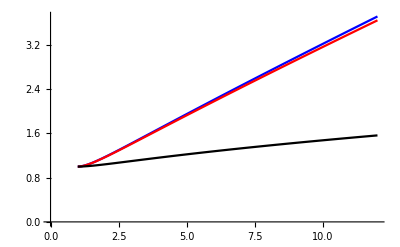

```mathematica
Plot[Evaluate@Table[ρ2[R0, α]^α,{α, {influenzaalpha, omicronalpha, measlesalpha}}],{R0, 1, 12}, PlotRange->{0, Automatic}, PlotStyle->{{Blue}, {Red}, {Black}}]
```

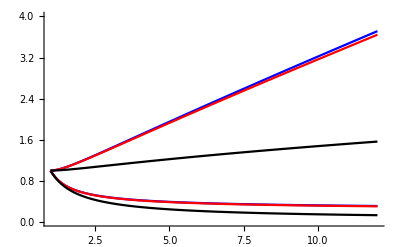

```mathematica
Show[
Plot[Evaluate@Table[ρ1[R0, α]^α,{α, {influenzaalpha, omicronalpha, measlesalpha}}],{R0, 1, 12}, PlotRange->{0, Automatic}, PlotStyle->{Blue, Red, Black}], 
Plot[Evaluate@Table[ρ2[R0, α]^α,{α, {influenzaalpha, omicronalpha, measlesalpha}}],{R0, 1, 12}, PlotRange->{0, Automatic}, PlotStyle->{Blue, Red, Black}], PlotRange->{0, 4}]
```

Plots of Var[W] as a function of psi:

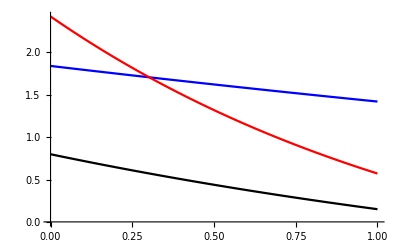

```mathematica
Plot[
Evaluate@(((ρ1[#[[1]],#[[2]]]^(#[[2]]) + ρ2[#[[1]],#[[2]]]^((1-ψ)#[[2]]) - 1)/(1 - ρ1[#[[1]],#[[2]]]^(#[[2]]))) &/@ ({{influenzaR0, influenzaalpha}, {omicronR0, omicronalpha}, {measlesR0, measlesalpha}})),
{ψ, 0, 1}, PlotStyle->{Blue, Red, Black}]
```

Plot of Mode[ϛ] as a function of psi:

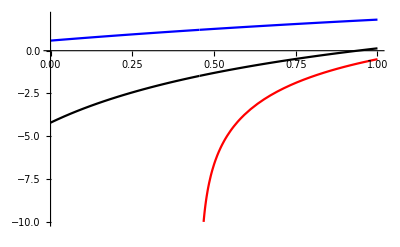

```mathematica
Plot[Evaluate@(1/(#[[4]])Log[(2 (1 - ρ1[#[[1]],#[[2]]]^(#[[2]])) - #[[3]] ρ2[#[[1]], #[[2]]]^((1 - ψ) #[[2]]))/(#[[3]] (1 - ρ1[#[[1]], #[[2]]]^(#[[2]])))] &/@ {{influenzaR0, influenzaalpha, influenzapest, influenzar},
{omicronR0, omicronalpha, omicronpest, omicronr},
{measlesR0, measlesalpha, measlespest, measlesr}}),{ψ,0,1}, PlotStyle->{Blue, Red, Black}, PlotRange->{-10,2}]
```

Why isn’t the gamma approximation a good one for exponential-looking distributions? I need to work clearly through the Mode derivation and make sure I understand it.